## First Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]]
```

{A_M_Pred,A_Av_M_Obs,A_F_Pred,A_Av_F_Obs,B_M_Pred,B_Av_M_Obs,B_F_Pred,B_Av_F_Obs,C_M_Pred,C_Av_M_Obs,C_F_Pred,C_Av_F_Obs,D_M_Pred,D_Av_M_Obs,D_F_Pred,D_Av_F_Obs}

{{0.047619,0.047619,0,0,0.2,0.2,0,0,0.333333,0.333333,0,0,0.5,0.5,0,0},{0.0591818,0.08476,0,0.00025,0.217,0.270208,0,0.00152934,0.3255,0.401054,0,0.00367502,0.651,0.549596,0,0.0166616},{0.0750337,0.122258,0.000476079,0.00102083,0.255662,0.31739,0.00641045,0.00394758,0.363742,0.435863,0.0144535,0.0126913,0.611055,0.569134,0.0584705,0.0309902},{0.092911,0.15229,0.00100004,0.0034745,0.282319,0.327272,0.011337,0.0144152,0.375975,0.424509,0.0231909,0.027417,0.527658,0.451269,0.0840029,0.0544324},{0.112947,0.197691,0.00182965,0.00727579,0.300872,0.334421,0.0171257,0.0211839,0.375645,0.367229,0.0320932,0.038692,0.455204,0.384477,0.0985691,0.0706009},{0.134485,0.214025,0.00306144,0.0104468,0.310892,0.314694,0.0234157,0.0309273,0.365394,0.331076,0.0406306,0.0399378,0.389891,0.442187,0.106838,0.0820593},{0.156566,0.181537,0.0047819,0.0200168,0.313065,0.285798,0.0298539,0.0373203,0.348298,0.296654,0.0483707,0.0418002,0.33513,0.434656,0.109321,0.130763},{0.178034,0.2112,0.00704797,0.0221861,0.308701,0.333349,0.0361228,0.0450509,0.327109,0.303426,0.0549728,0.0658841,0.290079,0.481508,0.1081,0.189022},{0.197709,0.217405,0.00987116,0.0376065,0.299348,0.340555,0.0419477,0.0623628,0.304044,0.376694,0.0602223,0.103353,0.253313,0.477475,0.104713,0.156916}}

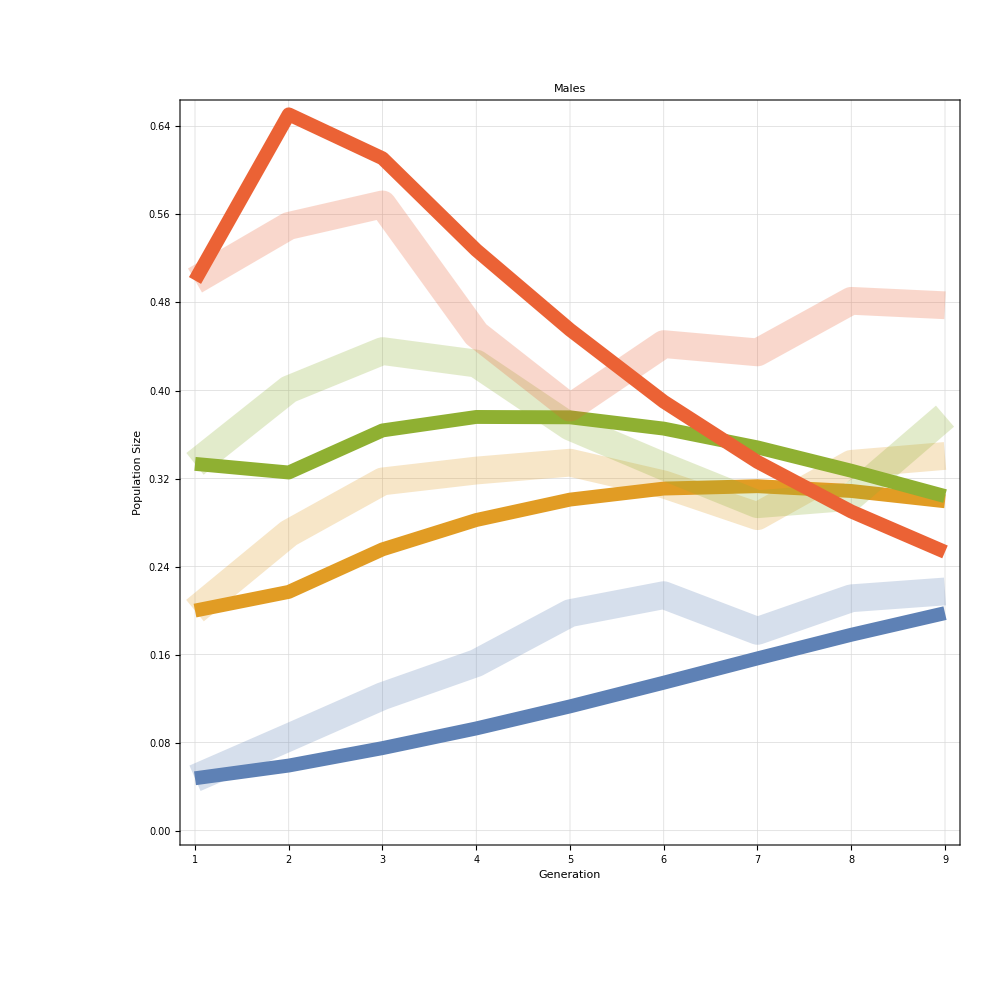
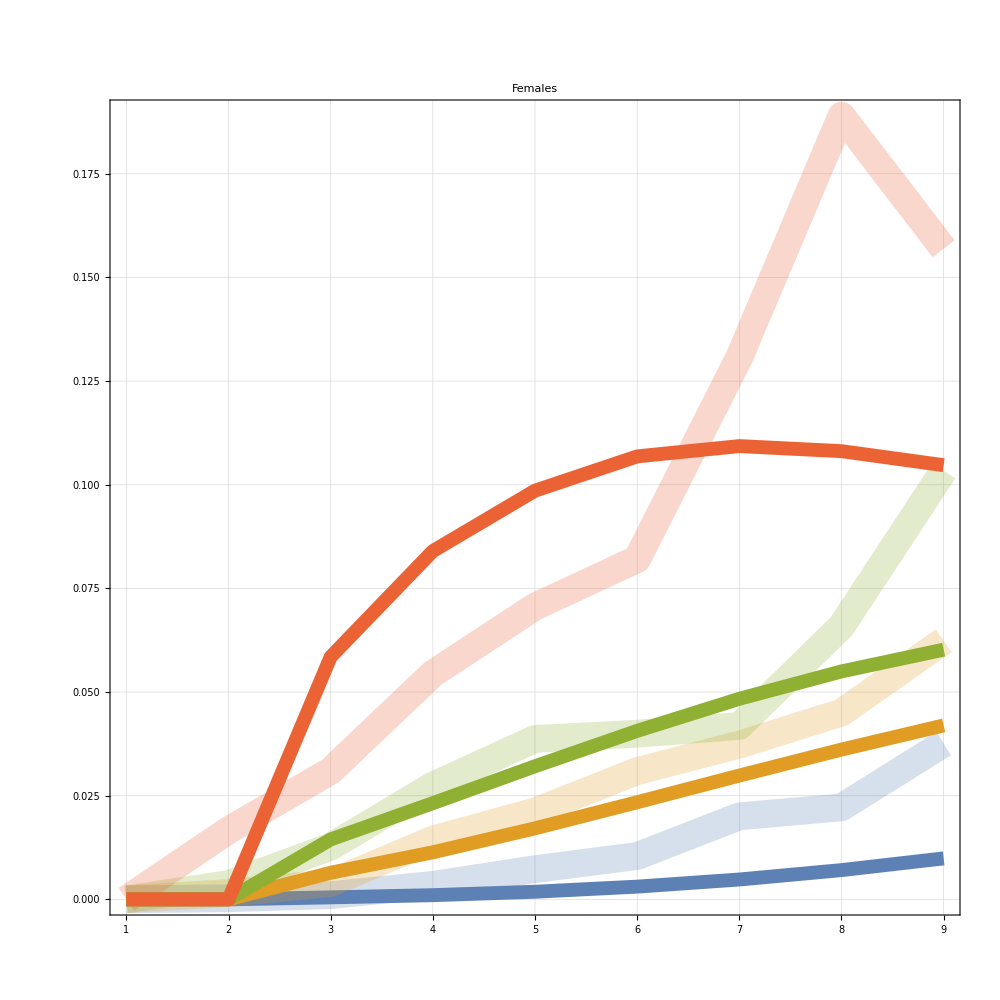
-Graphics- | -Graphics- |

experimentsGrid.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"A_M_Pred","A_Av_M_Obs","B_M_Pred","B_Av_M_Obs","C_M_Pred","C_Av_M_Obs","D_M_Pred","D_Av_M_Obs"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Generation","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Males",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"A_F_Pred","A_Av_F_Obs","B_F_Pred","B_Av_F_Obs","C_F_Pred","C_Av_F_Obs","D_F_Pred","D_Av_F_Obs"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Females",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;4]],{"1","2","3","4"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",35]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid.pdf",grid]
```

## Second Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit2.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]];
```

{A_Female_Pred,A_D_Allele_Pred,A_W_Allele_Pred,A_R_Allele_Pred,A_B_Allele_Pred,I_Female_Pred,I_D_Allele_Pred,I_W_Allele_Pred,I_R_Allele_Pred,I_B_Allele_Pred}

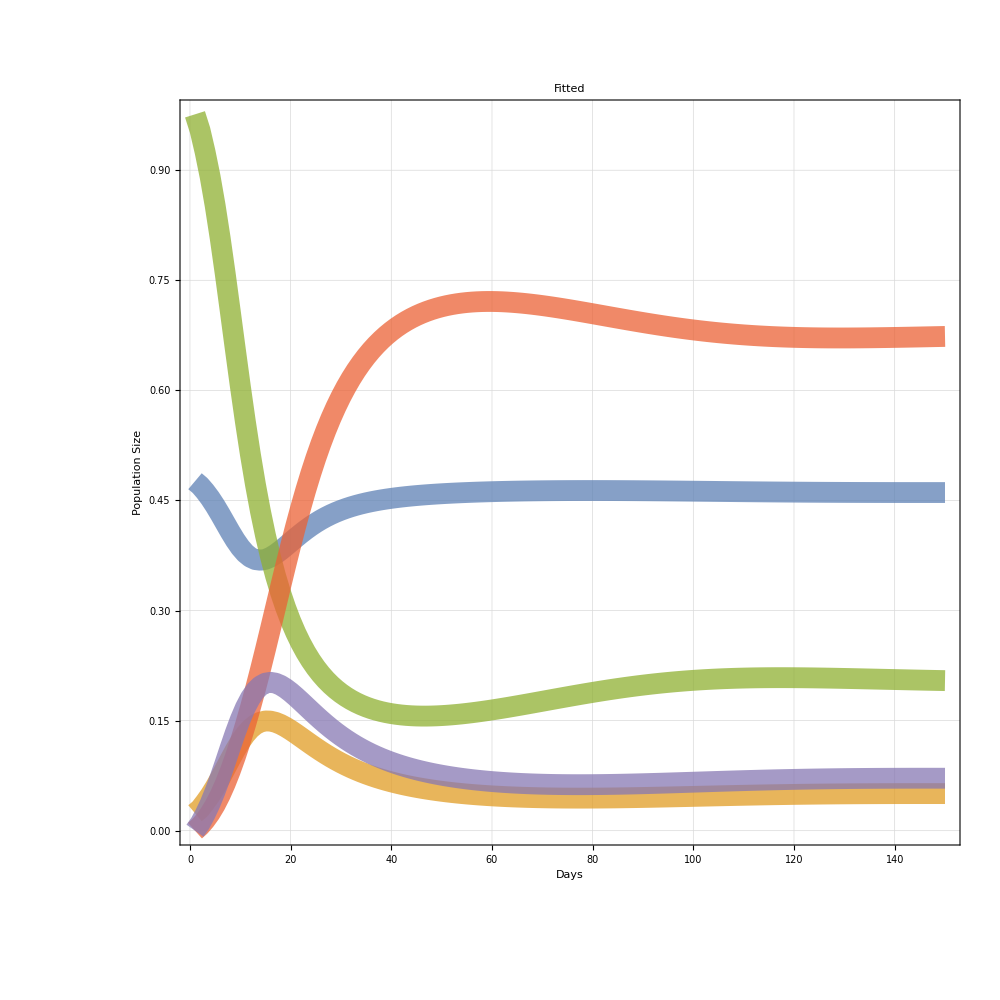
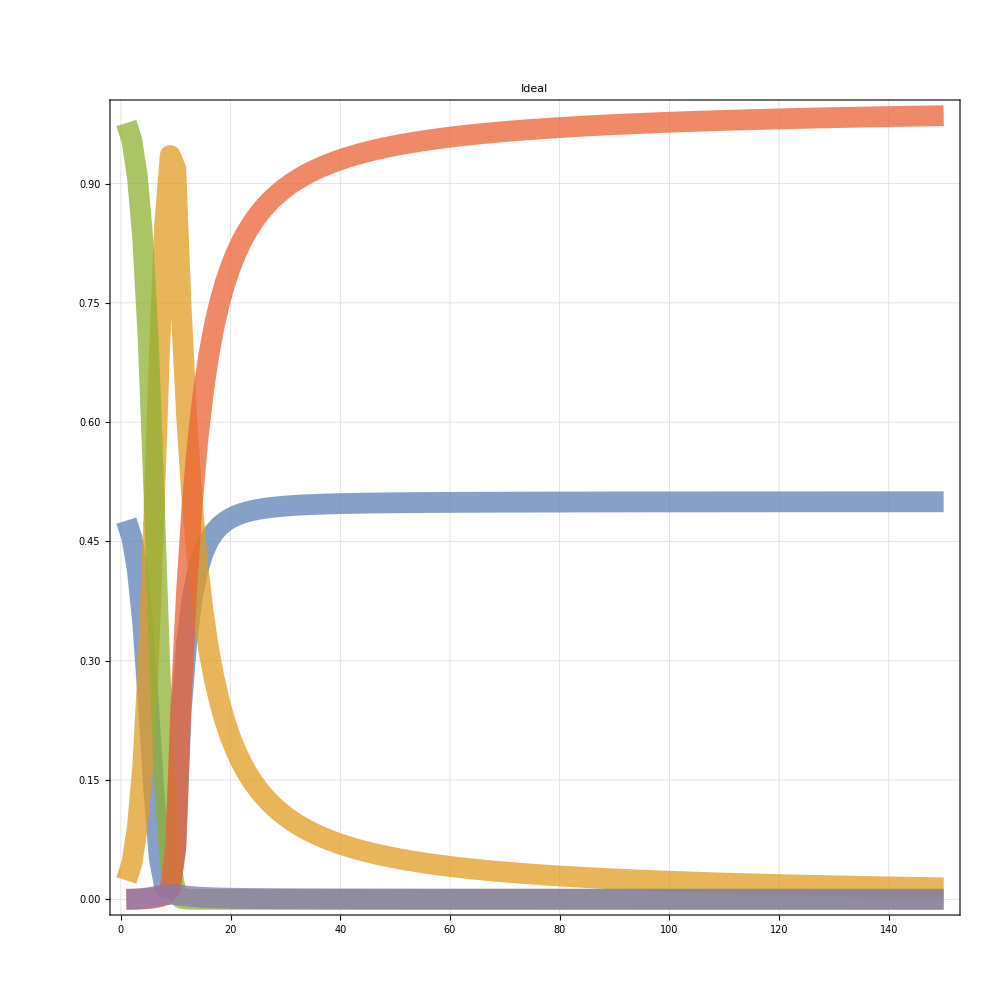
-Graphics- | -Graphics- |

experimentsGrid2.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"A_Female_Pred","A_D_Allele_Pred","A_W_Allele_Pred","A_R_Allele_Pred","A_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Days","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Fitted",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"I_Female_Pred","I_D_Allele_Pred","I_W_Allele_Pred","I_R_Allele_Pred","I_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Ideal",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;5]][[{4,1,2,3}]],{"B","D","Females","R","W"}[[{4,1,2,3}]],
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Genotype",35]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid2.pdf",grid]
```